0.000307929-1.91737951895799×10^-1409 ⅈ

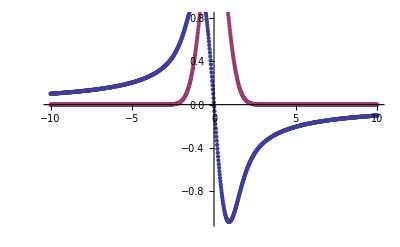

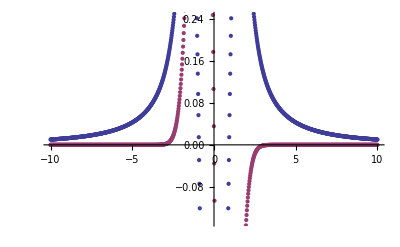

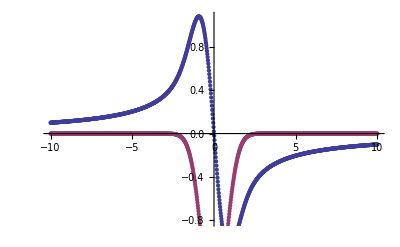

-Graphics-

```mathematica
Z[re_,im_,sgnKprl_]:= If[sgnKprl≥0,I Sqrt[Pi] Exp[-(re+ I im)^2] Erfc[-I (re+I im)],-I Sqrt[Pi] Exp[-(-1(re+ I im))^2] Erfc[-I (-1(re+I im))]];
Zp[re_,im_,sgnKprl_]:=If[sgnKprl≥0,-2 (1+(re+I im) Z[re,im]),-2 (1-(re+I im) (-1Z[re,im]))];
zReMin=-10;zReMax=10;nPtsRe=1000;
zRe=N[Table[re,{re,zReMin,zReMax,(zReMax-zReMin)/(nPtsRe-1)}]];
ZData=Z[zRe,0,1];
ZPData=Zp[zRe,0,1];
Zp[57.0,0,1]
(*ListPlot[{Re[ZData],Im[ZData]},DataRange->{zReMin,zReMax}]
ListPlot[{Re[ZPData],Im[ZPData]},DataRange->{zReMin,zReMax}]*)
Export["zFunction_kPrl_p.nc",{zRe,Re[ZData],Im[ZData],Re[ZPData],Im[ZPData]},{"Datasets",{"arg_re","Z_re","Z_im","Zp_re","Zp_im"}}];
ZData=Z[zRe,0,-1];
ZPData=Zp[zRe,0,-1];
(*ListPlot[{Re[ZData],Im[ZData]},DataRange->{zReMin,zReMax}]
ListPlot[{Re[ZPData],Im[ZPData]},DataRange->{zReMin,zReMax}]*)
Export["zFunction_kPrl_n.nc",{zRe,Re[ZData],Im[ZData],Re[ZPData],Im[ZPData]},{"Datasets",{"arg_re","Z_re","Z_im","Zp_re","Zp_im"}}];
```